```mathematica
$Assumptions={k ∈ Integers,n ∈ Integers,Ν∈Integers}
2-1/h^2((Sin[(π (2k+1)(n+1))/(2Ν-1)]-2 Sin[(π (2k+1)n)/(2Ν-1)]+Sin[(π (2k+1)(n-1))/(2Ν-1)])/Sin[(π (2k+1)n)/(2Ν-1)])//FullSimplify
```

{k∈ℤ,n∈ℤ,Ν∈ℤ}

(2 (1+h^2-Cos[(π+2 k π)/(1-2 Ν)]))/h^2

```mathematica
2-ⅇ^((π k ⅈ)/(Ν-1))-ⅇ^(-(π k ⅈ)/(Ν-1))//FullSimplify
```

2-2 Cos[(k π)/(-1+Ν)]

```mathematica
(13 q^5+(13+α)q^4+(α+7)q^3 +(α+7)q^2+(α+1)q+1)/(1+q)//Simplify
```

```mathematica
1+7 q^2+13 q^4+q α+q^3 α //TeXForm
```

\alpha  q^3+13 q^4+7 q^2+\alpha  q+1

```mathematica
f[z_,0]:=1+7 z^2+13 z^4+z α+z^3 α
```

```mathematica
f[z_,n_]:=1/z(Last[CoefficientList[f[z,n-1],z]]f[z,n-1]-First[CoefficientList[f[z,n-1],z]] z^Exponent[f[z,n-1],z] f[1/z,n-1])//Simplify
```

```mathematica
f[z,4]
```

4129544208384 (86436-1225 α^2+4 α^4)

```mathematica
Reduce[RealAbs[2 (-147+α^2)]>RealAbs[-7α],α]
```

α<-14||-21/2<α<21/2||α>14

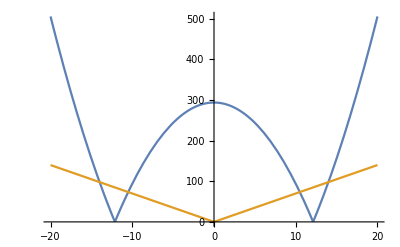

```mathematica
Plot[{RealAbs[2 (-147+α^2)],RealAbs[-7α]},{α,-20,20}]
```

```mathematica
1+7 q^2+13 q^4+q α+q^3 α /.α->-21/2//FullSimplify
```

1/2 (-1+q) (-2+q (19+q (5+26 q)))

```mathematica
1-13 q-7 q^2-7 q^3-q^4+13 q^5//FullSimplify
```

(1+q) (1+q (-14+q (7+q (-14+13 q))))

```mathematica
1+7 z^2+13 z^4+z α+z^3 α//TeXForm
```

\alpha  z^3+13 z^4+7 z^2+\alpha  z+1

```mathematica
-2+q (19+q (5+26 q))
```

```mathematica
-2+q (19+q (5+26 q))//Expand//TeXForm
```

26 q^3+5 q^2+19 q-2

```mathematica
A=({{1-q, -1}, {-2, -q}})
```

{{1-q,-1},{-2,-q}}

```mathematica
Solve[Det[A]==0,q]
```

{{q→-1},{q→2}}

```mathematica
Eigensystem[A]
```

{{7,-1},{{1,3},{3,1}}}

```mathematica
A=({{-2, 3}, {-3, 8}})
```

{{-2,3},{-3,8}}

```mathematica
Solve[{4a==3b+5,-6b+3a==30,3c==3d-6,-7d+3c+2==0},{a,b,c,d}]
```

{{a→-4,b→-7,c→-3,d→-1}}

```mathematica
A= ({{1000(1-Subscript[y, 1]^2), 1}, {-1, 0}})
```

{{1000 (1-y_1^2),1},{-1,0}}

```mathematica
Eigenvalues[A]//FullSimplify
```

{1/2 (1000-1000 y_1^2-√(-4+1000000 (-1+y_1^2)^2)),1/2 (1000-1000 y_1^2+√(-4+1000000 (-1+y_1^2)^2))}

```mathematica
$Assumptions={λ≥0,Λ≥0,Subscript[y, 1]∈Reals}
Reduce[{Re[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))]≤ -Λ,
RealAbs[Im[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))]]≤Λ,
Abs[1/2 (1000-1000 Subscript[y, 1]^2+√(-4+1000000 (-1+Subscript[y, 1]^2)^2))]≤λ},Subscript[y, 1]]
```

{λ≥0,Λ≥0,y_1∈ℝ}

```mathematica
Plot
```

Plot

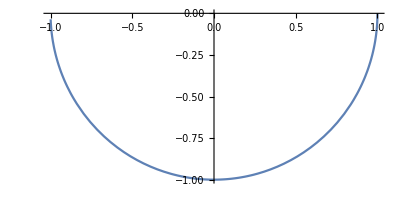

```mathematica
ParametricPlot[{Re[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))],Im[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))]},{Subscript[y, 1],-(√(501/5))/10,-(√(499/5))/10}]
```

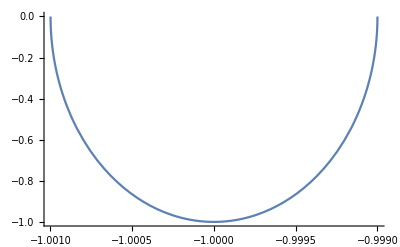

```mathematica
Plot[Im[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))],{Subscript[y, 1],-(√(501/5))/10,-(√(499/5))/10}]
```

```mathematica
Reduce[-4+1000000 (-1+Subscript[y, 1]^2)^2≤0,Subscript[y, 1]]//FullSimplify
```

-(√(501/5))/10≤y_1≤-(√(499/5))/10||(√(499/5))/10≤y_1≤(√(501/5))/10

```mathematica
Im[1/2 (1000-1000 Subscript[y, 1]^2-√(-4+1000000 (-1+Subscript[y, 1]^2)^2))]
```

1/2 Im[-1000 y_1^2-√(-4+1000000 (-1+y_1^2)^2)]

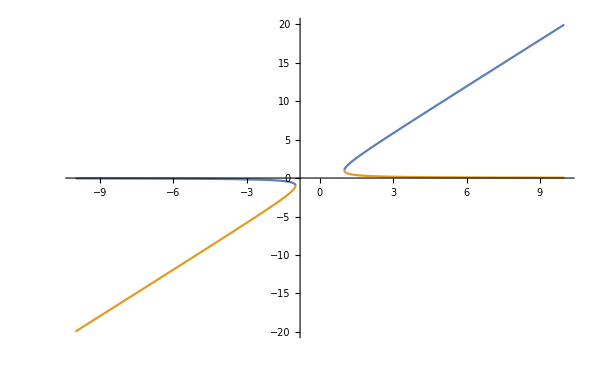

```mathematica
Show[Plot[{x+√(x^2-1),x-√(x^2-1)},{x,-10,-1},PlotRange->All],Plot[{x+√(x^2-1),x-√(x^2-1)},{x,1,10}]]
```

```mathematica
$Assumptions={x≤ -1}
```

{x≤-1}

```mathematica
(x-√(x^2-1))/(x+√(x^2-1))//FullSimplify
```

-1+2 x (x-√(-1+x^2))

```mathematica
-1+2 x (x-√(-1+x^2))/.x->500(1-Subscript[y, 1]^2)//FullSimplify//TeXForm
```

1000 \left(1-y_1^2\right) \left(-500 \left(y_1^2-1\right)-\sqrt{250000
   \left(y_1^2-1\right){}^2-1}\right)-1

```mathematica
Reduce[RealAbs[-1+1000 (1-Subscript[y, 1]^2) (500 (1-Subscript[y, 1]^2)-√(-1+250000 (1-Subscript[y, 1]^2)^2))]≤1/10,Subscript[y, 1]]//FullSimplify
```

-1/100 √(10000-11 √10)≤y_1≤1/100 √(10000-11 √10)

```mathematica
-1+2 x (x-√(-1+x^2))//TeXForm
```

2 x \left(x-\sqrt{x^2-1}\right)-1

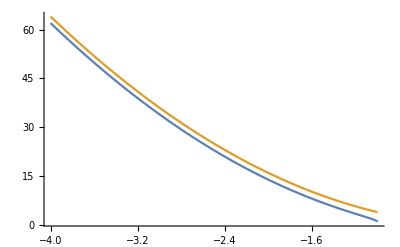

```mathematica
Plot[{(x-√(x^2-1))/(x+√(x^2-1)),4 x^2},{x,-4,-1},PlotRange->All]
```

```mathematica
Series[-1+2 x (x-√(-1+x^2)),x->-∞]//Normal//FullSimplify
```

4 x^2

```mathematica
-1+2 x (x-√(-1+x^2))//TeXForm
```

2 x \left(x-\sqrt{x^2-1}\right)-1

```mathematica
4 x^2/. x->500(1-Subscript[y, 1]^2)
```

1000000 (1-y_1^2)^2

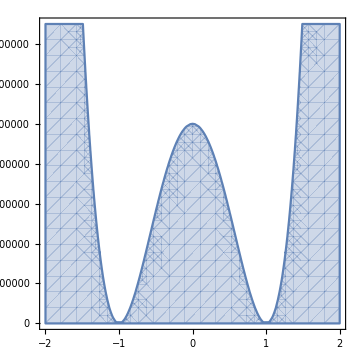

```mathematica
RegionPlot[1000000 (1-Subscript[y, 1]^2)^2≥α,{Subscript[y, 1],-2,2},{α,0,1.5 10^6},ImageSize->Medium,BaseStyle->{FontFamily->"CMU Serif"},FrameLabel->MaTeX@{"y_1","\\alpha"},LabelStyle->{NumberPoint->","}]
```

```mathematica
$Assumptions={α>0}
```

{α>0}

```mathematica
Reduce[1000000 (1-Subscript[y, 1]^2)^2≥α,Subscript[y, 1]]
```

y_1∈ℝ&&(α≤0||(0<α<1000000&&(y_1≤-√(1+(√α)/1000)||-√(1-(√α)/1000)≤y_1≤√(1-(√α)/1000)||y_1≥√(1+(√α)/1000)))||(α==1000000&&(y_1≤-√2||y_1==0||y_1≥√2))||(α>1000000&&(y_1≤-√(1+(√α)/1000)||y_1≥√(1+(√α)/1000))))

```mathematica
<<MaTeX`
```

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{mathtext}" ,
"\\usepackage[T2A]{fontenc}",
"\\usepackage[utf8]{inputenc}",
"\\usepackage[english,russian]{babel}",
"\\usepackage{units}"}];
```

```mathematica
1000000 (1-Subscript[y, 1]^2)^2≥α//TeXForm
```

1000000 \left(1-y_1^2\right){}^2\geq \alpha

```mathematica
Series[u[Subscript[x, n]+h],{h,0,4}]//Normal/.{u[Subscript[x, n]]-> Subscript[u, n],u'[Subscript[x, n]]->f[Subscript[x, n],Subscript[u, n]],u''[Subscript[x, n]]-> D[f[x,u[x]], x]/.{u'[x]->f[x,u[x]]}/.x->Subscript[x, n]
```

u_n[x_n]+h u_n'[x_n]+1/2 h^2 u_n''[x_n]+1/6 h^3 u_n^(3)[x_n]+1/24 h^4 u_n^(4)[x_n]

```mathematica
Series[u[Subscript[x, n]+h],{h,0,4}]//Normal
```

u[x_n]+h u'[x_n]+1/2 h^2 u''[x_n]+1/6 h^3 u^(3)[x_n]+1/24 h^4 u^(4)[x_n]

```mathematica
Subscript[u, n][Subscript[x, n]]+h Subscript[u, n]'[Subscript[x, n]]+1/2 h^2 Subscript[u, n]''[Subscript[x, n]]+1/6 h^3 Derivative[3][Subscript[u, n]][Subscript[x, n]]+1/24 h^4 Derivative[4][Subscript[u, n]][Subscript[x, n]]/. Derivative[i_][Subscript[u, n]][_]:>   Derivative[i-1][f][x]
```

```mathematica
h f[x]+Subscript[u, n][Subscript[x, n]]+1/2 h^2 f'[x]+1/6 h^3 f''[x]+1/24 h^4 Derivative[3][f][x,]
```

```mathematica
CoefficientList[Normal[Series[u[Subscript[x, n]+h],{h,0,4}]]//.Derivative[i_][u][_] ->  D[f[Subscript[x, n],u[Subscript[x, n]]],{Subscript[x, n],i-1}]/.u[Subscript[x, n]]->Subscript[u, n],h]
```

{u_n,f[x_n,u_n],1/2 (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]),1/6 (f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n]),1/24 ((f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) f^(1,1)[x_n,u_n]+2 (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(0,1)[x_n,u_n] (f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n])+f[x_n,u_n] f^(2,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(1,2)[x_n,u_n]+f^(2,1)[x_n,u_n])+f[x_n,u_n] (f^(0,2)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,2)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,3)[x_n,u_n]+f^(1,2)[x_n,u_n])+f^(2,1)[x_n,u_n])+f^(3,0)[x_n,u_n])}

```mathematica
Normal[Series[u[x+h],{h,0,4}]](*/.u'[x]->f[x,u[x]]*)
```

u[x]+h u'[x]+1/2 h^2 u''[x]+1/6 h^3 u^(3)[x]+1/24 h^4 u^(4)[x]

```mathematica
h f[x,u[x]]+u[x]+1/2 h^2 f'[x,u[x]]+1/6 h^3 f''[x,u[x]]+1/24 h^4 Derivative[3][f][x,u[x]] //Evaluate
```

h f[x,u[x]]+u[x]+1/2 h^2 f'[x,u[x]]+1/6 h^3 f''[x,u[x]]+1/24 h^4 f^(3)[x,u[x]]

```mathematica
FullForm[Series[u[Subscript[x, n]+h],{h,0,4}]//Normal]
```

Plus[u[Subscript[x,n]],Times[h,Derivative[1][u][Subscript[x,n]]],Times[Rational[1,2],Power[h,2],Derivative[2][u][Subscript[x,n]]],Times[Rational[1,6],Power[h,3],Derivative[3][u][Subscript[x,n]]],Times[Rational[1,24],Power[h,4],Derivative[4][u][Subscript[x,n]]]]

```mathematica
FullForm[Series[u[Subscript[x, n]+h],{h,0,4}]//Normal]
```

Plus[u[Subscript[x,n]],Times[h,Derivative[1][u][Subscript[x,n]]],Times[Rational[1,2],Power[h,2],Derivative[2][u][Subscript[x,n]]],Times[Rational[1,6],Power[h,3],Derivative[3][u][Subscript[x,n]]],Times[Rational[1,24],Power[h,4],Derivative[4][u][Subscript[x,n]]]]

```mathematica
Unevaluated[D[f[x,u[x]], x]] //FullForm
```

Unevaluated[D[f[x,u[x]],x]]

```mathematica
D[f[x,u[x]], x]/.{u'[x]->f[x,u[x]]}/.x->Subscript[x, n]
```

f[x_n,u[x_n]] f^(0,1)[x_n,u[x_n]]+f^(1,0)[x_n,u[x_n]]

```mathematica
D[f[x,u[x]], {x,2}]/.{u'[x]->f[x,u[x]],u''[x]->{D[f[x,u[x]], x]/.{u'[x]->f[x,u[x]]}}}
```

{f^(0,1)[x,u[x]] (f[x,u[x]] f^(0,1)[x,u[x]]+f^(1,0)[x,u[x]])+f[x,u[x]] f^(1,1)[x,u[x]]+f[x,u[x]] (f[x,u[x]] f^(0,2)[x,u[x]]+f^(1,1)[x,u[x]])+f^(2,0)[x,u[x]]}

```mathematica
s=2;
Subscript[k, i_]:=f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]]
Subscript[y, n+1]=Subscript[y, n]+h ∑_(i=1)^s Subscript[b, i] Subscript[k, i]
```

```mathematica
D[f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]], h]/.h->0
```

(a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(0,1)[x_n,y_n]+c_i f^(1,0)[x_n,y_n]

```mathematica
D[f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]], {h,2}]/.h->0
```

(2 a_(i,1) k_1'[0]+2 a_(i,2) k_2'[0]) f^(0,1)[x_n,y_n]+(a_(i,1) k_1[0]+a_(i,2) k_2[0]) ((a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(0,2)[x_n,y_n]+c_i f^(1,1)[x_n,y_n])+c_i ((a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(1,1)[x_n,y_n]+c_i f^(2,0)[x_n,y_n])

```mathematica
Subscript[y, i]=.
```

```mathematica
f[Subscript[x, n]+Subscript[c, i] h ϵ,Subscript[y, n]+h ϵ ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]]
```

```mathematica
s=2;
CoefficientList[Subscript[y, n]+h∑_(i=1)^s (Subscript[b, i] Normal[Series[f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{ε,0,1}]]/.{ε->1})//FullSimplify,h]
```

{y_n,f[x_n,y_n] (b_1+b_2),(b_1 (k_1 a_(1,1)+k_2 a_(1,2))+b_2 (k_1 a_(2,1)+k_2 a_(2,2))) f^(0,1)[x_n,y_n]+(b_1 c_1+b_2 c_2) f^(1,0)[x_n,y_n]}

{k_1→(f[x_n,y_n] (-1+h (-a_(1,2)+a_(2,2)) f^(0,1)[x_n,y_n])+h (-c_1+h (-c_2 a_(1,2)+c_1 a_(2,2)) f^(0,1)[x_n,y_n]) f^(1,0)[x_n,y_n])/(-1+h f^(0,1)[x_n,y_n] (a_(1,1)+a_(2,2)+h (a_(1,2) a_(2,1)-a_(1,1) a_(2,2)) f^(0,1)[x_n,y_n])),k_2→(f[x_n,y_n] (1+h (-a_(1,1)+a_(2,1)) f^(0,1)[x_n,y_n])+h (c_2+h (-c_2 a_(1,1)+c_1 a_(2,1)) f^(0,1)[x_n,y_n]) f^(1,0)[x_n,y_n])/(1-h (a_(1,1)+a_(2,2)) f^(0,1)[x_n,y_n]+h^2 (-a_(1,2) a_(2,1)+a_(1,1) a_(2,2)) (f^(0,1)[x_n,y_n])^2)}

```mathematica
Solve[Table[Subscript[k, i]==Series[f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{ε,0,1}],{i,2}],Table[Subscript[k, i],{i,2}]]
```

```mathematica
Series[f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{ε,0,1}]
```

f[x_n,y_n]+(h (k_1 a_(i,1)+k_2 a_(i,2)) f^(0,1)[x_n,y_n]+h c_i f^(1,0)[x_n,y_n]) ε+O[ε]^2

```mathematica
AsymptoticSolve[Table[Subscript[k, i]==f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{i,2}],Table[Subscript[k, i],{i,2}],ε->0]
```

AsymptoticSolve[{k_1==f[h ε c_1+x_n,y_n+h ε (k_1 a_(1,1)+k_2 a_(1,2))],k_2==f[h ε c_2+x_n,y_n+h ε (k_1 a_(2,1)+k_2 a_(2,2))]},{k_1,k_2},ε→0]

```mathematica
s=2;
F[h_,i_]:=f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]]
(*rule=Solve[Table[Subscript[k, i]==Normal[Series[f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{ε,0,1}]]/.{ε->1},{i,2}],Table[Subscript[k, i],{i,2}]]//FullSimplify//Flatten;*)
list1=CoefficientList[Normal[Series[Subscript[y, n]+h ∑_(i=1)^s Subscript[b, i] Subscript[k, i][h],{h,0,4}]]//.{Derivative[m_][Subscript[k, i_]][_] ->  Derivative[m,0][F][0,i],Subscript[k, i_][0]->f[Subscript[x, n],Subscript[y, n]],Subscript[k, i_]->f[Subscript[x, n],Subscript[y, n]]},h];
(*list1=CoefficientList[Normal[Series[Subscript[y, n]+h∑_(i=1)^s (Subscript[b, i] Normal[Series[f[Subscript[x, n]+Subscript[c, i] h ε,Subscript[y, n]+h ε ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{ε,0,1}]]/.{ε->1})/.rule,{h,0,4}]],h];*)
list2=CoefficientList[Normal[Series[u[Subscript[x, n]+h],{h,0,4}]]//.Derivative[i_][u][_] ->  D[f[Subscript[x, n],u[Subscript[x, n]]],{Subscript[x, n],i-1}]/.u[Subscript[x, n]]->Subscript[u, n],h]
```

{u_n,f[x_n,u_n],1/2 (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]),1/6 (f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n]),1/24 ((f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) f^(1,1)[x_n,u_n]+2 (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(0,1)[x_n,u_n] (f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n])+f[x_n,u_n] f^(2,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(1,2)[x_n,u_n]+f^(2,1)[x_n,u_n])+f[x_n,u_n] (f^(0,2)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,2)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,3)[x_n,u_n]+f^(1,2)[x_n,u_n])+f^(2,1)[x_n,u_n])+f^(3,0)[x_n,u_n])}

```mathematica
(*Solve[*)list1==list2//Thread//FullSimplify(*,{Subscript[u, n],Subscript[b, 1],Subscript[b, 2],Subscript[c, 1],Subscript[c, 2],Subscript[a, 1,1],Subscript[a, 1,2],Subscript[a, 2,1],Subscript[a, 2,2]}]*)
```

{u_n==y_n,f[x_n,u_n]==f[x_n,y_n] (b_1+b_2),f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]==2 f[x_n,y_n] (b_1 (a_(1,1)+a_(1,2))+b_2 (a_(2,1)+a_(2,2))) f^(0,1)[x_n,y_n]+2 (b_1 c_1+b_2 c_2) f^(1,0)[x_n,y_n],f[x_n,u_n]^2 f^(0,2)[x_n,u_n]+f^(0,1)[x_n,u_n] f^(1,0)[x_n,u_n]+f[x_n,u_n] ((f^(0,1)[x_n,u_n])^2+2 f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n]==3 f[x_n,y_n]^2 (b_1 (a_(1,1)+a_(1,2))^2+b_2 (a_(2,1)+a_(2,2))^2) f^(0,2)[x_n,y_n]+6 f[x_n,y_n] (b_1 c_1 (a_(1,1)+a_(1,2))+b_2 c_2 (a_(2,1)+a_(2,2))) f^(1,1)[x_n,y_n]+3 (b_1 c_1^2+b_2 c_2^2) f^(2,0)[x_n,y_n],f[x_n,u_n]^3 f^(0,3)[x_n,u_n]+f^(1,0)[x_n,u_n] ((f^(0,1)[x_n,u_n])^2+3 f^(1,1)[x_n,u_n])+f[x_n,u_n]^2 (4 f^(0,1)[x_n,u_n] f^(0,2)[x_n,u_n]+3 f^(1,2)[x_n,u_n])+f^(0,1)[x_n,u_n] f^(2,0)[x_n,u_n]+f[x_n,u_n] ((f^(0,1)[x_n,u_n])^3+5 f^(0,1)[x_n,u_n] f^(1,1)[x_n,u_n]+3 (f^(0,2)[x_n,u_n] f^(1,0)[x_n,u_n]+f^(2,1)[x_n,u_n]))+f^(3,0)[x_n,u_n]==4 (f[x_n,y_n]^3 (b_1 (a_(1,1)+a_(1,2))^3+b_2 (a_(2,1)+a_(2,2))^3) f^(0,3)[x_n,y_n]+3 f[x_n,y_n]^2 (b_1 c_1 (a_(1,1)+a_(1,2))^2+b_2 c_2 (a_(2,1)+a_(2,2))^2) f^(1,2)[x_n,y_n]+3 f[x_n,y_n] (b_1 c_1^2 (a_(1,1)+a_(1,2))+b_2 c_2^2 (a_(2,1)+a_(2,2))) f^(2,1)[x_n,y_n]+(b_1 c_1^3+b_2 c_2^3) f^(3,0)[x_n,y_n])}

```mathematica
list1=CoefficientList[Normal[Series[Subscript[y, n]+h ∑_(i=1)^s Subscript[b, i] f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{h,0,4}]],h]/.{Subscript[k, i_]->f[Subscript[x, n],Subscript[y, n]]}(*//.Derivative[m_][Subscript[k, i_]][_] ->  Derivative[m,0][F][h,i],h]*)
```

{y_n,f[x_n,y_n] b_1+f[x_n,y_n] b_2,b_1 ((f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2)) f^(0,1)[x_n,y_n]+c_1 f^(1,0)[x_n,y_n])+b_2 ((f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2)) f^(0,1)[x_n,y_n]+c_2 f^(1,0)[x_n,y_n]),b_1 (1/2 (f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2))^2 f^(0,2)[x_n,y_n]+c_1 (f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2)) f^(1,1)[x_n,y_n]+1/2 c_1^2 f^(2,0)[x_n,y_n])+b_2 (1/2 (f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2))^2 f^(0,2)[x_n,y_n]+c_2 (f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2)) f^(1,1)[x_n,y_n]+1/2 c_2^2 f^(2,0)[x_n,y_n]),b_1 (1/6 (f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2))^3 f^(0,3)[x_n,y_n]+1/2 c_1 (f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2))^2 f^(1,2)[x_n,y_n]+1/2 c_1^2 (f[x_n,y_n] a_(1,1)+f[x_n,y_n] a_(1,2)) f^(2,1)[x_n,y_n]+1/6 c_1^3 f^(3,0)[x_n,y_n])+b_2 (1/6 (f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2))^3 f^(0,3)[x_n,y_n]+1/2 c_2 (f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2))^2 f^(1,2)[x_n,y_n]+1/2 c_2^2 (f[x_n,y_n] a_(2,1)+f[x_n,y_n] a_(2,2)) f^(2,1)[x_n,y_n]+1/6 c_2^3 f^(3,0)[x_n,y_n])}

```mathematica
D[f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j]],{h,1}]/.h->0
```

(k_1 a_(i,1)+k_2 a_(i,2)) f^(0,1)[x_n,y_n]+c_i f^(1,0)[x_n,y_n]

```mathematica
Simplify[{Subscript[u, n]==Subscript[y, n],f[Subscript[x, n],Subscript[u, n]]==f[Subscript[x, n],Subscript[y, n]] (Subscript[b, 1]+Subscript[b, 2]),f[Subscript[x, n],Subscript[y, n]] (Subscript[b, 1] (Subscript[a, 1,1]+Subscript[a, 1,2])+Subscript[b, 2] (Subscript[a, 2,1]+Subscript[a, 2,2])) Derivative[0,1][f][Subscript[x, n],Subscript[y, n]]+(Subscript[b, 1] Subscript[c, 1]+Subscript[b, 2] Subscript[c, 2]) Derivative[1,0][f][Subscript[x, n],Subscript[y, n]]==1/2 (f[Subscript[x, n],Subscript[u, n]] Derivative[0,1][f][Subscript[x, n],Subscript[u, n]]+Derivative[1,0][f][Subscript[x, n],Subscript[u, n]]),Derivative[0,1][f][Subscript[x, n],Subscript[y, n]] (f[Subscript[x, n],Subscript[y, n]] (Subscript[b, 1] (Subscript[a, 1,1]^2+Subscript[a, 1,1] Subscript[a, 1,2]+Subscript[a, 1,2] (Subscript[a, 2,1]+Subscript[a, 2,2]))+Subscript[b, 2] (Subscript[a, 1,1] Subscript[a, 2,1]+Subscript[a, 1,2] Subscript[a, 2,1]+Subscript[a, 2,2] (Subscript[a, 2,1]+Subscript[a, 2,2]))) Derivative[0,1][f][Subscript[x, n],Subscript[y, n]]+(Subscript[b, 1] (Subscript[c, 1] Subscript[a, 1,1]+Subscript[c, 2] Subscript[a, 1,2])+Subscript[b, 2] (Subscript[c, 1] Subscript[a, 2,1]+Subscript[c, 2] Subscript[a, 2,2])) Derivative[1,0][f][Subscript[x, n],Subscript[y, n]])==1/6 (f[Subscript[x, n],Subscript[u, n]]^2 Derivative[0,2][f][Subscript[x, n],Subscript[u, n]]+Derivative[0,1][f][Subscript[x, n],Subscript[u, n]] Derivative[1,0][f][Subscript[x, n],Subscript[u, n]]+f[Subscript[x, n],Subscript[u, n]] ((Derivative[0,1][f][Subscript[x, n],Subscript[u, n]])^2+2 Derivative[1,1][f][Subscript[x, n],Subscript[u, n]])+Derivative[2,0][f][Subscript[x, n],Subscript[u, n]]),(Derivative[0,1][f][Subscript[x, n],Subscript[y, n]])^2 (f[Subscript[x, n],Subscript[y, n]] (Subscript[b, 2] (Subscript[a, 1,1]^2 Subscript[a, 2,1]+Subscript[a, 1,1] Subscript[a, 2,1] (Subscript[a, 1,2]+Subscript[a, 2,2])+Subscript[a, 2,2]^2 (Subscript[a, 2,1]+Subscript[a, 2,2])+Subscript[a, 1,2] Subscript[a, 2,1] (Subscript[a, 2,1]+2 Subscript[a, 2,2]))+Subscript[b, 1] (Subscript[a, 1,1]^3+Subscript[a, 1,1]^2 Subscript[a, 1,2]+Subscript[a, 1,1] Subscript[a, 1,2] (2 Subscript[a, 2,1]+Subscript[a, 2,2])+Subscript[a, 1,2] (Subscript[a, 1,2] Subscript[a, 2,1]+Subscript[a, 2,2] (Subscript[a, 2,1]+Subscript[a, 2,2])))) Derivative[0,1][f][Subscript[x, n],Subscript[y, n]]+(Subscript[b, 1] (Subscript[c, 1] (Subscript[a, 1,1]^2+Subscript[a, 1,2] Subscript[a, 2,1])+Subscript[c, 2] Subscript[a, 1,2] (Subscript[a, 1,1]+Subscript[a, 2,2]))+Subscript[b, 2] (Subscript[c, 1] Subscript[a, 2,1] (Subscript[a, 1,1]+Subscript[a, 2,2])+Subscript[c, 2] (Subscript[a, 1,2] Subscript[a, 2,1]+Subscript[a, 2,2]^2))) Derivative[1,0][f][Subscript[x, n],Subscript[y, n]])==1/24 (f[Subscript[x, n],Subscript[u, n]]^3 Derivative[0,3][f][Subscript[x, n],Subscript[u, n]]+(Derivative[0,1][f][Subscript[x, n],Subscript[u, n]])^2 Derivative[1,0][f][Subscript[x, n],Subscript[u, n]]+3 Derivative[1,0][f][Subscript[x, n],Subscript[u, n]] Derivative[1,1][f][Subscript[x, n],Subscript[u, n]]+f[Subscript[x, n],Subscript[u, n]]^2 (4 Derivative[0,1][f][Subscript[x, n],Subscript[u, n]] Derivative[0,2][f][Subscript[x, n],Subscript[u, n]]+3 Derivative[1,2][f][Subscript[x, n],Subscript[u, n]])+Derivative[0,1][f][Subscript[x, n],Subscript[u, n]] Derivative[2,0][f][Subscript[x, n],Subscript[u, n]]+f[Subscript[x, n],Subscript[u, n]] ((Derivative[0,1][f][Subscript[x, n],Subscript[u, n]])^3+5 Derivative[0,1][f][Subscript[x, n],Subscript[u, n]] Derivative[1,1][f][Subscript[x, n],Subscript[u, n]]+3 (Derivative[0,2][f][Subscript[x, n],Subscript[u, n]] Derivative[1,0][f][Subscript[x, n],Subscript[u, n]]+Derivative[2,1][f][Subscript[x, n],Subscript[u, n]]))+Derivative[3,0][f][Subscript[x, n],Subscript[u, n]])}/.Subscript[y, n]->Subscript[u, n],ForAll[{m,p},Derivative[m,p][f][Subscript[x, n],Subscript[u, n]]≠0]]
```

{True,f[x_n,u_n] (-1+b_1+b_2)==0,f[x_n,u_n] (-1+2 b_1 (a_(1,1)+a_(1,2))+2 b_2 (a_(2,1)+a_(2,2))) f^(0,1)[x_n,u_n]+(-1+2 b_1 c_1+2 b_2 c_2) f^(1,0)[x_n,u_n]==0,f[x_n,u_n]^2 f^(0,2)[x_n,u_n]+f^(2,0)[x_n,u_n]==(-1+6 b_1 (c_1 a_(1,1)+c_2 a_(1,2))+6 b_2 (c_1 a_(2,1)+c_2 a_(2,2))) f^(0,1)[x_n,u_n] f^(1,0)[x_n,u_n]+f[x_n,u_n] ((-1+6 b_1 (a_(1,1)^2+a_(1,1) a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2)))+6 b_2 (a_(1,1) a_(2,1)+a_(1,2) a_(2,1)+a_(2,2) (a_(2,1)+a_(2,2)))) (f^(0,1)[x_n,u_n])^2-2 f^(1,1)[x_n,u_n]),f[x_n,u_n]^3 f^(0,3)[x_n,u_n]+3 f^(1,0)[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n]^2 (4 f^(0,1)[x_n,u_n] f^(0,2)[x_n,u_n]+3 f^(1,2)[x_n,u_n])+f^(0,1)[x_n,u_n] f^(2,0)[x_n,u_n]+f^(3,0)[x_n,u_n]==(-1+24 b_1 (c_1 (a_(1,1)^2+a_(1,2) a_(2,1))+c_2 a_(1,2) (a_(1,1)+a_(2,2)))+24 b_2 (c_1 a_(2,1) (a_(1,1)+a_(2,2))+c_2 (a_(1,2) a_(2,1)+a_(2,2)^2))) (f^(0,1)[x_n,u_n])^2 f^(1,0)[x_n,u_n]+f[x_n,u_n] ((-1+24 b_2 (a_(1,1)^2 a_(2,1)+a_(1,1) a_(2,1) (a_(1,2)+a_(2,2))+a_(2,2)^2 (a_(2,1)+a_(2,2))+a_(1,2) a_(2,1) (a_(2,1)+2 a_(2,2)))+24 b_1 (a_(1,1)^3+a_(1,1)^2 a_(1,2)+a_(1,1) a_(1,2) (2 a_(2,1)+a_(2,2))+a_(1,2) (a_(1,2) a_(2,1)+a_(2,2) (a_(2,1)+a_(2,2))))) (f^(0,1)[x_n,u_n])^3-5 f^(0,1)[x_n,u_n] f^(1,1)[x_n,u_n]-3 (f^(0,2)[x_n,u_n] f^(1,0)[x_n,u_n]+f^(2,1)[x_n,u_n]))}

```mathematica
Flatten[{list1-list2//Thread}/.Subscript[y, n]->Subscript[u, n]]
```

{0,-f[x_n,u_n]+f[x_n,u_n] b_1+f[x_n,u_n] b_2,1/2 (-f[x_n,u_n] f^(0,1)[x_n,u_n]-f^(1,0)[x_n,u_n])+b_1 ((f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2)) f^(0,1)[x_n,u_n]+c_1 f^(1,0)[x_n,u_n])+b_2 ((f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2)) f^(0,1)[x_n,u_n]+c_2 f^(1,0)[x_n,u_n]),1/6 (-f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])-f[x_n,u_n] f^(1,1)[x_n,u_n]-f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])-f^(2,0)[x_n,u_n])+b_1 (1/2 (f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2))^2 f^(0,2)[x_n,u_n]+c_1 (f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2)) f^(1,1)[x_n,u_n]+1/2 c_1^2 f^(2,0)[x_n,u_n])+b_2 (1/2 (f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2))^2 f^(0,2)[x_n,u_n]+c_2 (f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2)) f^(1,1)[x_n,u_n]+1/2 c_2^2 f^(2,0)[x_n,u_n]),1/24 (-(f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) f^(1,1)[x_n,u_n]-2 (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n]) (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])-f^(0,1)[x_n,u_n] (f^(0,1)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,1)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,2)[x_n,u_n]+f^(1,1)[x_n,u_n])+f^(2,0)[x_n,u_n])-f[x_n,u_n] f^(2,1)[x_n,u_n]-f[x_n,u_n] (f[x_n,u_n] f^(1,2)[x_n,u_n]+f^(2,1)[x_n,u_n])-f[x_n,u_n] (f^(0,2)[x_n,u_n] (f[x_n,u_n] f^(0,1)[x_n,u_n]+f^(1,0)[x_n,u_n])+f[x_n,u_n] f^(1,2)[x_n,u_n]+f[x_n,u_n] (f[x_n,u_n] f^(0,3)[x_n,u_n]+f^(1,2)[x_n,u_n])+f^(2,1)[x_n,u_n])-f^(3,0)[x_n,u_n])+b_1 (1/6 (f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2))^3 f^(0,3)[x_n,u_n]+1/2 c_1 (f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2))^2 f^(1,2)[x_n,u_n]+1/2 c_1^2 (f[x_n,u_n] a_(1,1)+f[x_n,u_n] a_(1,2)) f^(2,1)[x_n,u_n]+1/6 c_1^3 f^(3,0)[x_n,u_n])+b_2 (1/6 (f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2))^3 f^(0,3)[x_n,u_n]+1/2 c_2 (f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2))^2 f^(1,2)[x_n,u_n]+1/2 c_2^2 (f[x_n,u_n] a_(2,1)+f[x_n,u_n] a_(2,2)) f^(2,1)[x_n,u_n]+1/6 c_2^3 f^(3,0)[x_n,u_n])}

```mathematica
Map[#==0&,DeleteCases[CoefficientList[#,set]&/@Flatten[{list1-list2//Thread}/.Subscript[y, n]->Subscript[u, n]],0,∞]//Flatten]//FullSimplify
```

{b_1+b_2==1,2 b_1 c_1+2 b_2 c_2==1,2 b_1 (a_(1,1)+a_(1,2))+2 b_2 (a_(2,1)+a_(2,2))==1,3 b_1 c_1^2+3 b_2 c_2^2==1,6 b_1 (c_1 a_(1,1)+c_2 a_(1,2))+6 b_2 (c_1 a_(2,1)+c_2 a_(2,2))==1,3 b_1 c_1 (a_(1,1)+a_(1,2))+3 b_2 c_2 (a_(2,1)+a_(2,2))==1,6 b_2 ((a_(1,1)+a_(1,2)) a_(2,1)+a_(2,1) a_(2,2)+a_(2,2)^2)+6 b_1 (a_(1,1)^2+a_(1,1) a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2)))==1,3 b_1 (a_(1,1)+a_(1,2))^2+3 b_2 (a_(2,1)+a_(2,2))^2==1,4 b_1 c_1^3+4 b_2 c_2^3==1,8 b_1 c_1 (c_1 a_(1,1)+c_2 a_(1,2))+8 b_2 c_2 (c_1 a_(2,1)+c_2 a_(2,2))==1,12 (b_1 (c_1^2 a_(1,1)+c_2^2 a_(1,2))+b_2 (c_1^2 a_(2,1)+c_2^2 a_(2,2)))==1,b_1 (c_1 (a_(1,1)^2+a_(1,2) a_(2,1))+c_2 a_(1,2) (a_(1,1)+a_(2,2)))+b_2 (c_1 a_(2,1) (a_(1,1)+a_(2,2))+c_2 (a_(1,2) a_(2,1)+a_(2,2)^2))==1/24,4 b_1 c_1^2 (a_(1,1)+a_(1,2))+4 b_2 c_2^2 (a_(2,1)+a_(2,2))==1,8 b_1 (a_(1,1)+a_(1,2)) (c_1 a_(1,1)+c_2 a_(1,2))+8 b_2 (a_(2,1)+a_(2,2)) (c_1 a_(2,1)+c_2 a_(2,2))==1,b_2 ((c_1+c_2) (a_(1,1)+a_(1,2)) a_(2,1)+2 c_2 a_(2,1) a_(2,2)+2 c_2 a_(2,2)^2)+b_1 (c_2 a_(1,2) (a_(2,1)+a_(2,2))+c_1 (2 a_(1,1)^2+2 a_(1,1) a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2))))==5/24,b_2 (a_(1,1)^2 a_(2,1)+a_(1,1) a_(2,1) (a_(1,2)+a_(2,2))+a_(2,2)^2 (a_(2,1)+a_(2,2))+a_(1,2) a_(2,1) (a_(2,1)+2 a_(2,2)))+b_1 (a_(1,1)^3+a_(1,1)^2 a_(1,2)+a_(1,1) a_(1,2) (2 a_(2,1)+a_(2,2))+a_(1,2) (a_(1,2) a_(2,1)+a_(2,2) (a_(2,1)+a_(2,2))))==1/24,4 b_1 c_1 (a_(1,1)+a_(1,2))^2+4 b_2 c_2 (a_(2,1)+a_(2,2))^2==1,3 b_2 ((a_(1,1)+a_(1,2)) a_(2,1) (a_(1,1)+a_(1,2)+2 a_(2,1))+a_(2,1) (2 (a_(1,1)+a_(1,2))+3 a_(2,1)) a_(2,2)+6 a_(2,1) a_(2,2)^2+3 a_(2,2)^3)+3 b_1 (3 a_(1,1)^3+6 a_(1,1)^2 a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2)) (2 a_(1,2)+a_(2,1)+a_(2,2))+a_(1,1) a_(1,2) (3 a_(1,2)+2 (a_(2,1)+a_(2,2))))==1,4 b_1 (a_(1,1)+a_(1,2))^3+4 b_2 (a_(2,1)+a_(2,2))^3==1}

```mathematica
set=Table[Derivative[m,p][f][Subscript[x, n],Subscript[u, n]],{m,0,3},{p,0,3-m}]//Flatten
```

{f[x_n,u_n],f^(0,1)[x_n,u_n],f^(0,2)[x_n,u_n],f^(0,3)[x_n,u_n],f^(1,0)[x_n,u_n],f^(1,1)[x_n,u_n],f^(1,2)[x_n,u_n],f^(2,0)[x_n,u_n],f^(2,1)[x_n,u_n],f^(3,0)[x_n,u_n]}

```mathematica
list1=CoefficientList[Normal[Series[Subscript[y, n]+h ∑_(i=1)^s Subscript[b, i] f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]],{h,0,4}]]//.{Derivative[i_][Subscript[k, j_]][_] ->Derivative[i,0][F][0,j],Subscript[k, i_][0]->f[Subscript[x, n],Subscript[y, n]]},h];
```

```mathematica
Normal[Series[D[(f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]]), h],{h,0,0}]]
```

(a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(0,1)[x_n,y_n]+c_i f^(1,0)[x_n,y_n]

```mathematica
D[(f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]]), h]/.h->0
```

(a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(0,1)[x_n,y_n]+c_i f^(1,0)[x_n,y_n]

```mathematica
D[(f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]]), {h,2}]/.h->0
```

(2 a_(i,1) k_1'[0]+2 a_(i,2) k_2'[0]) f^(0,1)[x_n,y_n]+(a_(i,1) k_1[0]+a_(i,2) k_2[0]) ((a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(0,2)[x_n,y_n]+c_i f^(1,1)[x_n,y_n])+c_i ((a_(i,1) k_1[0]+a_(i,2) k_2[0]) f^(1,1)[x_n,y_n]+c_i f^(2,0)[x_n,y_n])

```mathematica
//.Derivative[i_][Subscript[k, j_]][_] ->Derivative[i,0][F][0,j]
```

```mathematica
F[h_,i_]:=f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]]
```

```mathematica
Derivative[1,0][F][0,1]
```

(a_(1,1) k_1[0]+a_(1,2) k_2[0]) f^(0,1)[x_n,y_n]+c_1 f^(1,0)[x_n,y_n]

```mathematica
s=2;
F[h_,i_]:=f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]]
list1=CoefficientList[Normal[Series[Subscript[y, n]+h ∑_(i=1)^s Subscript[b, i] f[Subscript[x, n]+Subscript[c, i] h,Subscript[y, n]+h ∑_(j=1)^s Subscript[a, i,j] Subscript[k, j][h]],{h,0,4}]]//.{Derivative[i_][Subscript[k, j_]][_] ->Derivative[i,0][F][0,j],Subscript[k, i_][0]->f[Subscript[x, n],Subscript[y, n]]},h];
list2=CoefficientList[Normal[Series[u[Subscript[x, n]+h],{h,0,4}]]//.Derivative[i_][u][_] ->  D[f[Subscript[x, n],u[Subscript[x, n]]],{Subscript[x, n],i-1}]/.u[Subscript[x, n]]->Subscript[u, n],h];
set=Table[Derivative[m,p][f][Subscript[x, n],Subscript[u, n]],{m,0,3},{p,0,3-m}]//Flatten;
Map[#==0&,DeleteCases[CoefficientList[#,set]&/@Flatten[{list1-list2//Thread}/.Subscript[y, n]->Subscript[u, n]],0,∞]//Flatten]//Simplify
```

{b_1+b_2==1,2 b_1 c_1+2 b_2 c_2==1,2 b_1 (a_(1,1)+a_(1,2))+2 b_2 (a_(2,1)+a_(2,2))==1,3 b_1 c_1^2+3 b_2 c_2^2==1,6 b_1 (c_1 a_(1,1)+c_2 a_(1,2))+6 b_2 (c_1 a_(2,1)+c_2 a_(2,2))==1,3 b_1 c_1 (a_(1,1)+a_(1,2))+3 b_2 c_2 (a_(2,1)+a_(2,2))==1,6 b_1 (a_(1,1)^2+a_(1,1) a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2)))+6 b_2 (a_(1,1) a_(2,1)+a_(1,2) a_(2,1)+a_(2,2) (a_(2,1)+a_(2,2)))==1,3 b_1 (a_(1,1)+a_(1,2))^2+3 b_2 (a_(2,1)+a_(2,2))^2==1,4 b_1 c_1^3+4 b_2 c_2^3==1,8 b_1 c_1 (c_1 a_(1,1)+c_2 a_(1,2))+8 b_2 c_2 (c_1 a_(2,1)+c_2 a_(2,2))==1,12 (b_1 (c_1^2 a_(1,1)+c_2^2 a_(1,2))+b_2 (c_1^2 a_(2,1)+c_2^2 a_(2,2)))==1,b_1 (c_1 (a_(1,1)^2+a_(1,2) a_(2,1))+c_2 a_(1,2) (a_(1,1)+a_(2,2)))+b_2 (c_1 a_(2,1) (a_(1,1)+a_(2,2))+c_2 (a_(1,2) a_(2,1)+a_(2,2)^2))==1/24,4 b_1 c_1^2 (a_(1,1)+a_(1,2))+4 b_2 c_2^2 (a_(2,1)+a_(2,2))==1,8 b_1 (a_(1,1)+a_(1,2)) (c_1 a_(1,1)+c_2 a_(1,2))+8 b_2 (a_(2,1)+a_(2,2)) (c_1 a_(2,1)+c_2 a_(2,2))==1,b_1 (c_2 a_(1,2) (a_(2,1)+a_(2,2))+c_1 (2 a_(1,1)^2+2 a_(1,1) a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2))))+b_2 (c_1 (a_(1,1)+a_(1,2)) a_(2,1)+c_2 (a_(1,1) a_(2,1)+a_(1,2) a_(2,1)+2 a_(2,2) (a_(2,1)+a_(2,2))))==5/24,b_2 (a_(1,1)^2 a_(2,1)+a_(1,1) a_(2,1) (a_(1,2)+a_(2,2))+a_(2,2)^2 (a_(2,1)+a_(2,2))+a_(1,2) a_(2,1) (a_(2,1)+2 a_(2,2)))+b_1 (a_(1,1)^3+a_(1,1)^2 a_(1,2)+a_(1,1) a_(1,2) (2 a_(2,1)+a_(2,2))+a_(1,2) (a_(1,2) a_(2,1)+a_(2,2) (a_(2,1)+a_(2,2))))==1/24,4 b_1 c_1 (a_(1,1)+a_(1,2))^2+4 b_2 c_2 (a_(2,1)+a_(2,2))^2==1,3 b_2 (a_(1,1)^2 a_(2,1)+a_(1,2)^2 a_(2,1)+2 a_(1,2) a_(2,1) (a_(2,1)+a_(2,2))+3 a_(2,2) (a_(2,1)+a_(2,2))^2+2 a_(1,1) a_(2,1) (a_(1,2)+a_(2,1)+a_(2,2)))+3 b_1 (3 a_(1,1)^3+6 a_(1,1)^2 a_(1,2)+a_(1,2) (a_(2,1)+a_(2,2)) (2 a_(1,2)+a_(2,1)+a_(2,2))+a_(1,1) a_(1,2) (3 a_(1,2)+2 (a_(2,1)+a_(2,2))))==1,4 b_1 (a_(1,1)+a_(1,2))^3+4 b_2 (a_(2,1)+a_(2,2))^3==1}

```mathematica
Needs@"CellsToTeX`"
```

```mathematica
SetOptions[CellToTeX,"CurrentCellIndex"->Automatic];
ExportString[NotebookGet[nbObj]/.cell:Cell[_,__]:>Cell[CellToTeX[cell],"Final"],"TeX","FullDocument"->False,"ConversionRules"->{"Final"->Identity}]
```

\begin{mmaCell}[moredefined={s, F, list1, list2, set},morepattern={h_, i_, j_, \#},morefunctionlocal={i, h, j, m, p}]{Input}
  s=2;
  F[h_,i_]:=f[\mmaSub{x}{n}+\mmaSub{c}{\mmaPat{i}}\mmaPat{h},\mmaSub{y}{n}+\mmaPat{h} \mmaUnderOver{\(\pmb{\sum}\)}{j=1}{s}\mmaSub{a}{\mmaPat{i},j}\mmaSub{k}{j}[\mmaPat{h}]]
  list1=CoefficientList[Normal[Series[\mmaSub{y}{n}+h \mmaUnderOver{\(\pmb{\sum}\)}{i=1}{s}\mmaSub{b}{i}f[\mmaSub{x}{n}+\mmaSub{c}{i}h,\mmaSub{y}{n}+h
\mmaUnderOver{\(\pmb{\sum}\)}{j=1}{s}\mmaSub{a}{i,j}\mmaSub{k}{j}[h]],\{h,0,4\}]]//.\{Derivative[i_][\mmaSub{k}{j_}][_] \(\pmb{\to}\)Derivative[\mmaUnd{i},0][F][0,\mmaUnd{j}],\mmaSub{k}{i_}[0]\(\pmb{\to}\)f[\mmaSub{x}{n},\mmaSub{y}{n}]\},\mmaUnd{h}];
  list2=CoefficientList[Normal[Series[u[\mmaSub{x}{n}+h],\{h,0,4\}]]//.Derivative[i_][u][_] \(\pmb{\to}\)  D[f[\mmaSub{x}{n},u[\mmaSub{x}{n}]],\{\mmaSub{x}{n},\mmaUnd{i}-1\}]/.u[\mmaSub{x}{n}]\(\pmb{\to}\)\mmaSub{u}{n},\mmaUnd{h}];
  set=Table[Derivative[m,p][f][\mmaSub{x}{n},\mmaSub{u}{n}],\{m,0,3\},\{p,0,3-m\}]//Flatten;
  Map[#==0&,DeleteCases[CoefficientList[#,set]&/@Flatten[\{list1-list2//Thread\}/.\mmaSub{y}{n}\(\pmb{\to}\)\mmaSub{u}{n}],0,\mmaDef{\(\pmb{\infty}\)}]//Flatten]//Simplify
\end{mmaCell}

\begin{mmaCell}[addtoindex=5]{Output}
  \{\mmaSub{b}{1}+\mmaSub{b}{2}==1,2 \mmaSub{b}{1} \mmaSub{c}{1}+2 \mmaSub{b}{2} \mmaSub{c}{2}==1,2 \mmaSub{b}{1} (\mmaSub{a}{1,1}+\mmaSub{a}{1,2})+2
\mmaSub{b}{2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})==1,3 \mmaSub{b}{1} \mmaSubSup{c}{1}{2}+3 \mmaSub{b}{2} \mmaSubSup{c}{2}{2}==1,6 \mmaSub{b}{1} (\mmaSub{c}{1}
\mmaSub{a}{1,1}+\mmaSub{c}{2} \mmaSub{a}{1,2})+6 \mmaSub{b}{2} (\mmaSub{c}{1} \mmaSub{a}{2,1}+\mmaSub{c}{2} \mmaSub{a}{2,2})==1,3 \mmaSub{b}{1} \mmaSub{c}{1}
(\mmaSub{a}{1,1}+\mmaSub{a}{1,2})+3 \mmaSub{b}{2} \mmaSub{c}{2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})==1,6 \mmaSub{b}{1} (\mmaSubSup{a}{1,1}{2}+\mmaSub{a}{1,1}
\mmaSub{a}{1,2}+\mmaSub{a}{1,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2}))+6 \mmaSub{b}{2} (\mmaSub{a}{1,1} \mmaSub{a}{2,1}+\mmaSub{a}{1,2} \mmaSub{a}{2,1}+\mmaSub{a}{2,2}
(\mmaSub{a}{2,1}+\mmaSub{a}{2,2}))==1,3 \mmaSub{b}{1} \mmaSup{(\mmaSub{a}{1,1}+\mmaSub{a}{1,2})}{2}+3 \mmaSub{b}{2} \mmaSup{(\mmaSub{a}{2,1}+\mmaSub{a}{2,2})}{2}==1,4
\mmaSub{b}{1} \mmaSubSup{c}{1}{3}+4 \mmaSub{b}{2} \mmaSubSup{c}{2}{3}==1,8 \mmaSub{b}{1} \mmaSub{c}{1} (\mmaSub{c}{1} \mmaSub{a}{1,1}+\mmaSub{c}{2}
\mmaSub{a}{1,2})+8 \mmaSub{b}{2} \mmaSub{c}{2} (\mmaSub{c}{1} \mmaSub{a}{2,1}+\mmaSub{c}{2} \mmaSub{a}{2,2})==1,12 (\mmaSub{b}{1} (\mmaSubSup{c}{1}{2}
\mmaSub{a}{1,1}+\mmaSubSup{c}{2}{2} \mmaSub{a}{1,2})+\mmaSub{b}{2} (\mmaSubSup{c}{1}{2} \mmaSub{a}{2,1}+\mmaSubSup{c}{2}{2} \mmaSub{a}{2,2}))==1,\mmaSub{b}{1}
(\mmaSub{c}{1} (\mmaSubSup{a}{1,1}{2}+\mmaSub{a}{1,2} \mmaSub{a}{2,1})+\mmaSub{c}{2} \mmaSub{a}{1,2} (\mmaSub{a}{1,1}+\mmaSub{a}{2,2}))+\mmaSub{b}{2}
(\mmaSub{c}{1} \mmaSub{a}{2,1} (\mmaSub{a}{1,1}+\mmaSub{a}{2,2})+\mmaSub{c}{2} (\mmaSub{a}{1,2} \mmaSub{a}{2,1}+\mmaSubSup{a}{2,2}{2}))==\mmaFrac{1}{24},4
\mmaSub{b}{1} \mmaSubSup{c}{1}{2} (\mmaSub{a}{1,1}+\mmaSub{a}{1,2})+4 \mmaSub{b}{2} \mmaSubSup{c}{2}{2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})==1,8 \mmaSub{b}{1}
(\mmaSub{a}{1,1}+\mmaSub{a}{1,2}) (\mmaSub{c}{1} \mmaSub{a}{1,1}+\mmaSub{c}{2} \mmaSub{a}{1,2})+8 \mmaSub{b}{2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})
(\mmaSub{c}{1} \mmaSub{a}{2,1}+\mmaSub{c}{2} \mmaSub{a}{2,2})==1,\mmaSub{b}{1} (\mmaSub{c}{2} \mmaSub{a}{1,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})+\mmaSub{c}{1}
(2 \mmaSubSup{a}{1,1}{2}+2 \mmaSub{a}{1,1} \mmaSub{a}{1,2}+\mmaSub{a}{1,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})))+\mmaSub{b}{2} (\mmaSub{c}{1} (\mmaSub{a}{1,1}+\mmaSub{a}{1,2})
\mmaSub{a}{2,1}+\mmaSub{c}{2} (\mmaSub{a}{1,1} \mmaSub{a}{2,1}+\mmaSub{a}{1,2} \mmaSub{a}{2,1}+2 \mmaSub{a}{2,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})))==\mmaFrac{5}{24},\mmaSub{b}{2}
(\mmaSubSup{a}{1,1}{2} \mmaSub{a}{2,1}+\mmaSub{a}{1,1} \mmaSub{a}{2,1} (\mmaSub{a}{1,2}+\mmaSub{a}{2,2})+\mmaSubSup{a}{2,2}{2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})+\mmaSub{a}{1,2}
\mmaSub{a}{2,1} (\mmaSub{a}{2,1}+2 \mmaSub{a}{2,2}))+\mmaSub{b}{1} (\mmaSubSup{a}{1,1}{3}+\mmaSubSup{a}{1,1}{2} \mmaSub{a}{1,2}+\mmaSub{a}{1,1} \mmaSub{a}{1,2}
(2 \mmaSub{a}{2,1}+\mmaSub{a}{2,2})+\mmaSub{a}{1,2} (\mmaSub{a}{1,2} \mmaSub{a}{2,1}+\mmaSub{a}{2,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})))==\mmaFrac{1}{24},4
\mmaSub{b}{1} \mmaSub{c}{1} \mmaSup{(\mmaSub{a}{1,1}+\mmaSub{a}{1,2})}{2}+4 \mmaSub{b}{2} \mmaSub{c}{2} \mmaSup{(\mmaSub{a}{2,1}+\mmaSub{a}{2,2})}{2}==1,3
\mmaSub{b}{2} (\mmaSubSup{a}{1,1}{2} \mmaSub{a}{2,1}+\mmaSubSup{a}{1,2}{2} \mmaSub{a}{2,1}+2 \mmaSub{a}{1,2} \mmaSub{a}{2,1} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})+3
\mmaSub{a}{2,2} \mmaSup{(\mmaSub{a}{2,1}+\mmaSub{a}{2,2})}{2}+2 \mmaSub{a}{1,1} \mmaSub{a}{2,1} (\mmaSub{a}{1,2}+\mmaSub{a}{2,1}+\mmaSub{a}{2,2}))+3
\mmaSub{b}{1} (3 \mmaSubSup{a}{1,1}{3}+6 \mmaSubSup{a}{1,1}{2} \mmaSub{a}{1,2}+\mmaSub{a}{1,2} (\mmaSub{a}{2,1}+\mmaSub{a}{2,2}) (2 \mmaSub{a}{1,2}+\mmaSub{a}{2,1}+\mmaSub{a}{2,2})+\mmaSub{a}{1,1}
\mmaSub{a}{1,2} (3 \mmaSub{a}{1,2}+2 (\mmaSub{a}{2,1}+\mmaSub{a}{2,2})))==1,4 \mmaSub{b}{1} \mmaSup{(\mmaSub{a}{1,1}+\mmaSub{a}{1,2})}{3}+4 \mmaSub{b}{2}
\mmaSup{(\mmaSub{a}{2,1}+\mmaSub{a}{2,2})}{3}==1\}
\end{mmaCell}

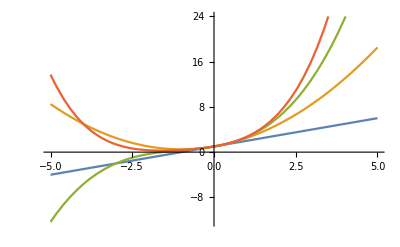

```mathematica
Plot [Table[Series[ⅇ^x,{x,0,n}]//Normal,{n,4}]//Evaluate,{x,-5,5}]
```

```mathematica
Table[Series[ⅇ^x,{x,0,n}]//Normal,{n,4}]
```

{1+x,1+x+x^2/2,1+x+x^2/2+x^3/6,1+x+x^2/2+x^3/6+x^4/24}

```mathematica
A=({{γ, 0}, {1-2γ, γ}});
b=({{1/2}, {1/2}});
e=({{1}, {1}});
Limit[Det[IdentityMatrix[2]-z A+z e.bᵀ]/Det[IdentityMatrix[2]-z A]//FullSimplify,z->-∞]
```

(1-4 γ+2 γ^2)/(2 γ^2)

```mathematica
Det[IdentityMatrix[2]-z A+z e.bᵀ]/Det[IdentityMatrix[2]-z A]≤1//FullSimplify
```

```mathematica
Reduce[RealAbs[Det[IdentityMatrix[2]-z A+z e.bᵀ]/Det[IdentityMatrix[2]-z A]]≤1&& Re[z]≤0,γ]
```

```mathematica
γ∈Reals&&((z<0&&γ≥(2+z)/(4 z))||z==0)
```

γ∈ℝ&&((z<0&&γ≥(2+z)/(4 z))||z==0)

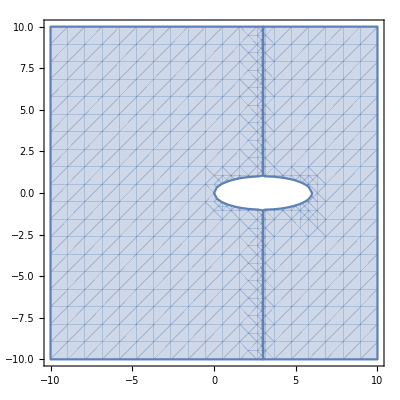

```mathematica
Show[RegionPlot[{Abs[(3-z+√(z^2-6z+1))/2]≤1}/.z->x+ⅈ y,{x,-10,10},{y,-10,10},BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->{NumberPoint->","}],RegionPlot[{Abs[(3-z-√(z^2-6z+1))/2]≤1}/.z->x+ⅈ y,{x,-10,10},{y,-10,10}]]
```

```mathematica
ColorData[97][4]
```

RGBColor[0.922526, 0.385626, 0.209179]

```mathematica
<<MaTeX``
```

```mathematica
A=({{(-√2)/2, 0}, {-1/2, 1-(√2)/2}});
b={√2,1-√2};
c={(-√2)/2,1/2-(√2)/2};
e={1,1};
b.c//FullSimplify
```

1/2-√2

```mathematica
c=.
```

```mathematica
Solve[b.{(-√2)/2,Subscript[c, 2]}==1/2,Subscript[c, 2]]//FullSimplify
```

{{c_2→-3/2 (1+√2)}}

```mathematica
Det[IdentityMatrix[2]-z A+z e.b]/Det[IdentityMatrix[2]-z A]//FullSimplify//TeXForm
```

-\frac{\left(\sqrt{2}-2\right) z^2+2 \left(1+\sqrt{2}\right)
   z+2}{\left(\sqrt{2}-1\right) (z-2) z-2}

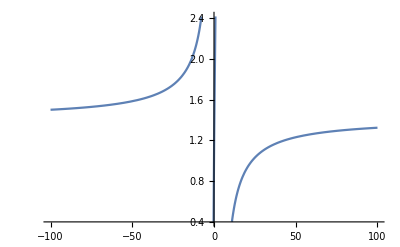

```mathematica
Plot[-(2+2 (1+√2) z+(-2+√2) z^2)/(-2+(-1+√2) (-2+z) z),{z,-100,100}]
```

```mathematica
Reduce[RealAbs[-(2+2 (1+√2) z+(-2+√2) z^2)/(-2+(-1+√2) (-2+z) z)]≤1,z]//TeXForm
```

2 \sqrt{2}-2 \sqrt{3}\leq z\leq 0\lor 2 \sqrt{2}+2 \sqrt{3}\leq z\leq
   -\frac{4}{2 \sqrt{2}-3}

```mathematica
sol=DSolve[{D[y[x], x]==1-2y[x],y[0]==1},y[x],x]
```

{{y[x]→1/2 ⅇ^(-2 x) (1+ⅇ^(2 x))}}

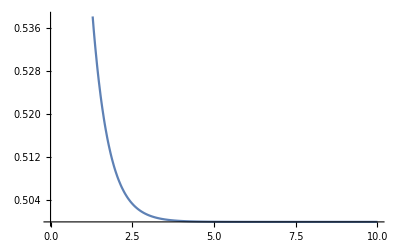

```mathematica
Plot[{1/2 ⅇ^(-2 x) (1+ⅇ^(2 x))},{x,0,10}]
```

```mathematica
Solve[q^2==1+2h(1-2q),q]
```

{{q→-2 h-√(1+2 h+4 h^2)},{q→-2 h+√(1+2 h+4 h^2)}}

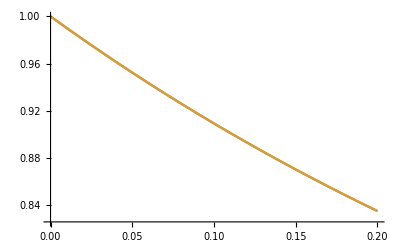

{{{0.,1.},{0.01,0.9901},{0.02,0.980396},{0.03,0.970884},{0.04,0.961561},{0.05,0.952422},{0.06,0.943464},{0.07,0.934683},{0.08,0.926076},{0.09,0.91764},{0.1,0.909371},{0.11,0.901265},{0.12,0.89332},{0.13,0.885532},{0.14,0.877899},{0.15,0.870417},{0.16,0.863082},{0.17,0.855893},{0.18,0.848847},{0.19,0.841939},{0.2,0.835169}},{{0.,1.},{0.01,0.990099},{0.02,0.980396},{0.03,0.970883},{0.04,0.961561},{0.05,0.952421},{0.06,0.943464},{0.07,0.934683},{0.08,0.926077},{0.09,0.917639},{0.1,0.909371},{0.11,0.901265},{0.12,0.89332},{0.13,0.885532},{0.14,0.877899},{0.15,0.870416},{0.16,0.863082},{0.17,0.855893},{0.18,0.848847},{0.19,0.841939},{0.2,0.835169}}}

```mathematica
Subscript[y, 0]=1.;
Subscript[y, 1]=a;
h=.01;
Subscript[y, n_]:=Subscript[y, n]=Subscript[y, n-2]+2.h(-2. Subscript[y, n-1]+1.)
ListLinePlot[Map[(Table[{h n,With[{a=#},Evaluate[Subscript[y, n]]]},{n,0,20}])&,{1/2(1-2 h+√(1+4 h^2)),0.5+0.5 ⅇ^(-2h)}]]
Map[(Table[{h n,With[{a=#},Evaluate[Subscript[y, n]]]},{n,0,20}])&,{1/2(1-2 h+√(1+4 h^2)),0.5+0.5 ⅇ^(-2h)}]
```

```mathematica
Subscript[y, 3]
```

0.02 (1.-2. (1.+0.02 (1.-2. a)))+a

```mathematica
<<MaTeX``
```

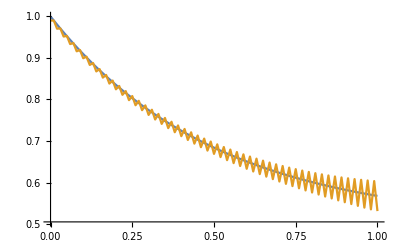

```mathematica
Clear["Global`*"]
Subscript[y, 1,0]=1.;
h=.01;
Subscript[y, 1,1]=1/2(1-2 h+√(1+4 h^2));
Subscript[y, 2,1]=0.5+0.5 ⅇ^(-2h);
Subscript[y, i_,n_]:=Subscript[y, i,n]=Subscript[y, i,n-2]+2.h(-2. Subscript[y, i,n-1]+1.)
ListLinePlot[Table[{h n,Subscript[y, i,n]},{i,2},{n,0,100}](*,Frame->True,FrameStyle->{Black},ImageSize->Medium,GridLines->Automatic,BaseStyle->{FontFamily->"CMU Serif"},FrameLabel->MaTeX@{"x","u(x)"},LabelStyle->{NumberPoint->","},PlotLegends->Placed[LineLegend[MaTeX@{"y_1=\\frac{1}{2} \\left( 
1-2h +\\sqrt{4h^2 +1} \\right)","y_1=\\frac{1}{2} \\left( 
1+e^{-2h} \\right)"},LegendFunction->(Framed[#,RoundingRadius->5,Background->White,FrameStyle->LightGray]&),LegendMargins->5],{Left,Center}]*)]
```

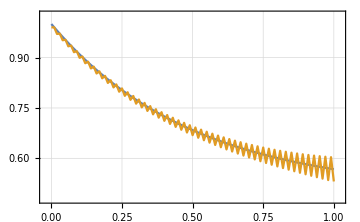

```mathematica
PlotLegends->Placed[LineLegend[MaTeX@{"y_1=\\frac{1}{2} \\left( 
1-2h +\\sqrt{4h^2 +1} \\right)","y_1=\\frac{1}{2} \\left( 
1+e^{-2h} \\right)"},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],{Left,Center}]
```

```mathematica
LineLegend[MaTeX@{"y_1=\\frac{1}{2} \\left( 
1-2h +\\sqrt{4h^2 +1} \\right)","y_1=\\frac{1}{2} \\left( 
1+e^{-2h} \\right)"},LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5]
```

```mathematica
Subscript[y, 1,0]=1.;
h=.01;
Subscript[y, 1,1]=1/2(1-2 h+√(1+4 h^2));
Subscript[y, 2,1]=0.5+0.5 ⅇ^(-2h);
Subscript[y, i_,n_]:=Subscript[y, i,n]=Subscript[y, i,n-2]+2.h(-2. Subscript[y, i,n-1]+1.)
ListLinePlot[Table[{h n,Subscript[y, i,n]},{i,2},{n,0,100}]]
```

-Graphics-

```mathematica
Subscript[y, 1,1]
```

0.9901

```mathematica
NumberForm[0.9900999900019994,16]
```

0.990099990002

```mathematica
Subscript[y, 2,1]
```

0.990099

```mathematica
NumberForm[0.9900993366533777,16]
```

0.990099336653378

```mathematica
ListPlot[Table[{n,Subscript[y, n]},{n,0,100}]]
```

```mathematica
Solve[1+2h(-2y+1)==-y,y]
```

{{y→(1+2 h)/(-1+4 h)}}

```mathematica
0==1+2h(-2 Subscript[y, 1]+1),
0==Subscript[y, 1]+2h
```

```mathematica
Subscript[y, n]=.
```

Unset::norep: Assignment on Subscript for y_n not found.

$Failed

```mathematica
Reduce[Subscript[y, 7]<Subscript[y, 6]<Subscript[y, 5]<Subscript[y, 3]<Subscript[y, 2],y]
```

(h≤-1/4&&y<(1+8 h+16 h^2+64 h^3)/(16 h+128 h^3))||(-1/4<h<Root-0.104Root[1+12 #1+48 #1^2+256 #1^3+256 #1^4+1024 #1^5&,1]-0.1040708852934339&&y<(1+10 h+48 h^2+160 h^3+256 h^4+512 h^5)/(1+12 h+48 h^2+256 h^3+256 h^4+1024 h^5))||(h>0&&(1+10 h+48 h^2+160 h^3+256 h^4+512 h^5)/(1+12 h+48 h^2+256 h^3+256 h^4+1024 h^5)<y<(1+12 h+72 h^2+256 h^3+768 h^4+1024 h^5+2048 h^6)/(1+12 h+96 h^2+256 h^3+1280 h^4+1024 h^5+4096 h^6))

```mathematica
1/2+α (-2 h-√(1+2 h+4 h^2))^n+β(-2 h+√(1+2 h+4 h^2))^n
```

```mathematica
q^2==1+2z//FullSimplify
```

q^2+h (-2+4 q)==1

```mathematica
Subscript[q, 1] Subscript[q, 2]=-1
```

```mathematica
Subscript[q, 1]+Subscript[q, 2]=-4h
```

```mathematica
1/2+α Subscript[q, 1]^n+β(-Subscript[q, 1])^-n
```

```mathematica
α+β=1/2
```

```mathematica
1/2+α Subscript[q, 1]^n+(1/2-α)(-Subscript[q, 1])^-n
```

```mathematica
Subscript[y, n_]:=Subscript[y, n-2]+2h(-2 Subscript[y, n-1]+1)
```

```mathematica
Subscript[y, 2]=1+2h(-y+1)
```

```mathematica
Subscript[y, 2]
```

1+2 h (1-2 y)

```mathematica
Subscript[y, 3]//FullSimplify
```

y+2 h (-1+h (-4+8 y))

```mathematica
Limit[α Subscript[q, 1]^n-α(-Subscript[q, 1])^-n,n->∞]
```

lim_(n→∞) (-α (-q_1)^-n+α q_1^n)

```mathematica
ConditionalExpression[∞, α>0&&Log[-(1+2 h)/Subscript[q, 1]]>0&&Log[-(1+2 h)/Subscript[q, 1]]<Log[Subscript[q, 1]]&&Log[Subscript[q, 1]]>0]
```

```mathematica
$Assumptions={h>0}
```

{h>0}

```mathematica
1/2+α Subscript[q, 1]^n+(1/2-α)((-1-2h)/Subscript[q, 1])^n//FullSimplify
```

1/2+(1/2-α) (-(1+2 h)/q_1)^n+α q_1^n

```mathematica
1/2(1+((-1-2h)/Subscript[q, 1])^n)+α(Subscript[q, 1]^n-((-1-2h)/Subscript[q, 1])^n)
```

```mathematica
Solve[1/2+α Subscript[q, 1]+(1/2-α)((-1-2h)/Subscript[q, 1])==y,α]
```

{{α→(1+2 h-q_1+2 y q_1)/(2 (1+2 h+q_1^2))}}

```mathematica
Limit[1/2+α Subscript[q, 1]^n+(1/2-α)((-1-2h)/Subscript[q, 1])^n/.α->(1+2 h-Subscript[q, 1]+2 y Subscript[q, 1])/(2 (1+2 h+Subscript[q, 1]^2)),n->∞]
```

```mathematica
Series[1/2+α Subscript[q, 1]^n+(1/2-α)((-1-2h)/Subscript[q, 1])^n/.α->(1+2 h-Subscript[q, 1]+2 y Subscript[q, 1])/(2 (1+2 h+Subscript[q, 1]^2)),{h,∞,0}]
```

(1/2 (1+q_1^n)+O[1/h]^1)+O[1/h]^1 ((-1-2 h)/q_1)^n

y(n+1)-y(n-1)=2h(1-2y(n)), y(0)=1, y(inf)=0

WolframAlphaQueryResults

```mathematica
Solve[q^2==1+2h(-2q),q]
```

{{q→-2 h-√(1+4 h^2)},{q→-2 h+√(1+4 h^2)}}

```mathematica
Reduce[{RealAbs[1+2z]≤1},h]
```

```mathematica
Reduce[-1≤-2 h≤0,h]
```

0≤h≤1/2

```mathematica
Solve[q^2==1+2h(-2q),q]
```

{{q→-2 h-√(1+4 h^2)},{q→-2 h+√(1+4 h^2)}}

```mathematica
h=.
```

```mathematica
$Assumptions={h>0}
```

{h>0}

```mathematica
Limit[α(-2 h+√(1+4 h^2))^n,n->∞]
```

ⅇ^(2 ⅈ Interval[{0,π}]) α ∞

```mathematica
Clear["Global`*"]
Solve[(1/2-β) Subscript[q, 1]+β Subscript[q, 2]+1/2==1/2(ⅇ^(-2h)+1),β]
```

{{β→(ⅇ^(-2 h) (-1+ⅇ^(2 h) q_1))/(2 (q_1-q_2))}}

```mathematica
Series[(ⅇ^(-2 h) (-1+ⅇ^(2 h) Subscript[q, 1]))/(2 (Subscript[q, 1]-Subscript[q, 2]))/.{Subscript[q, 1]->-2 h+√(1+4 h^2),Subscript[q, 2]->-2 h-√(1+4 h^2)}//FullSimplify,{h,0,3}]
```

h^3/3+O[h]^4

```mathematica
(ⅇ^(-2 h) (-1+ⅇ^(2 h) Subscript[q, 1]))/(2 (Subscript[q, 1]-Subscript[q, 2]))/.{Subscript[q, 1]->-2 h+√(1+4 h^2),Subscript[q, 2]->-2 h-√(1+4 h^2)}//FullSimplify
```

```mathematica
(-ⅇ^(-2 h)-2 h+√(1+4 h^2))/(4 √(1+4 h^2))//TeXForm
```

\frac{\sqrt{4 h^2+1}-2 h-e^{-2 h}}{4 \sqrt{4 h^2+1}}

```mathematica
Needs["CellsToTeX`"]
```

```mathematica
Cells
```

```mathematica
SetOptions[CellToTeX,"CurrentCellIndex"->Automatic];
ExportString[NotebookGet[nbObj]/.cell:Cell[_,__]:>Cell[CellToTeX[cell],"Final"],"TeX","FullDocument"->False,"ConversionRules"->{"Final"->Identity}]
```

SetOptions::optnf: CurrentCellIndex is not a known option for CellToTeX.

\[\text{NotebookGet}[\text{nbObj}]\]

```mathematica
y''[x]+(y'[x])^2-8 ⅇ^(y[x]-x)+23==0/.{y[x_]->v[x]+x,Derivative[i_][y][x]->D[v[x]+x,{x,i}]}
```

23-8 ⅇ^v[x]+(1+v'[x])^2+v''[x]==0

```mathematica
FullForm[y''[x]+(y'[x])^2-8 ⅇ^(y[x]-x)+23==0]
```

Equal[Plus[23,Times[-8,Power[E,Plus[Times[-1,x],y[x]]]],Power[Derivative[1][y][x],2],Derivative[2][y][x]],0]

```mathematica
Series[√(2(1+x)^2-1),{x,0,3}]
```

1+2 x-x^2+2 x^3+O[x]^4

```mathematica
y''[x]+(y'[x])^2-8 ⅇ^(y[x]-x)+23
```

```mathematica
Normal[Series[23-8 ⅇ^(v[x]ε)+(1+v'[x]ε)^2+v''[x]==0,{ε,0,1}]]/.ε->1
```

16-8 v[x]+2 v'[x]+v''[x]==0

```mathematica
DSolve[{16-8 v[x]+2 v'[x]+v''[x]==0,v[0]==0,v[1]==0},v[x],x]//FullSimplify
```

{{v[x]→(2 (1+ⅇ^2+ⅇ^4-ⅇ^(4-4 x)-ⅇ^(2 x) (1+ⅇ^2)))/(1+ⅇ^2+ⅇ^4)}}

```mathematica
(2 (1+ⅇ^2+ⅇ^4-ⅇ^(4-4 x)-ⅇ^(2 x) (1+ⅇ^2)))/(1+ⅇ^2+ⅇ^4)//TeXForm
```

\frac{2 \left(-e^{4-4 x}-\left(1+e^2\right) e^{2 x}+1+e^2+e^4\right)}{1+e^2+e^4}

```mathematica
Piecewise[{{1, i==1}, {0, True}}]
```

Piecewise[{{1, i==1}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{1,i==1}},0]]
```

Piecewise[{{1, i==1}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{-2-h^2 (10+0.0001 i^2),i==j},{1,i==1+j||1+i==j}},0]]
```

Piecewise[{{-2-h^2 (10+0.0001 i^2), i-j==0}, {1, i-j==-1||i-j==1}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{-2-0.0001 (10+0.0001 i^2),i==j},{1,i==1+j||1+i==j}},0]]
```

Piecewise[{{-2-0.0001 (10+0.0001 i^2), i-j==0}, {1, i-j==-1||i-j==1}, {0, True}}]

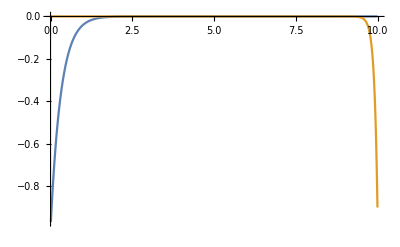

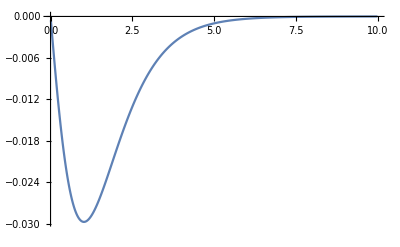

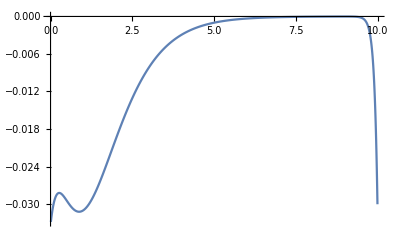

-Graphics-

```mathematica
Clear["Global`*"]
h=0.01;
Ν=10/h;
Subscript[x, i_]:=Subscript[x, i]=i h
Subscript[A, i_,j_]:=Subscript[A, i,j]=Piecewise[{{-2-h^2 (10+Subscript[x, i]^2),i==j},{1,i==1+j||1+i==j}},0]
Subscript[f, 1,i_]:=Subscript[f, 1,i]=Piecewise[{{1,i==1}},0]
Subscript[f, 2,i_]:=Subscript[f, 2,i]=Piecewise[{{1,i==Ν-1}},0]
Subscript[f, 3,i_]:=Subscript[f, 3,i]=h^2 Subscript[x, i] ⅇ^(-Subscript[x, i])
sol=Solve[Table[∑_(j=1)^(Ν-1) Subscript[A, i,j] Subscript[y, k,j]==Subscript[f, k,i],{i,Ν-1},{k,3}]//Flatten,Table[Subscript[y, k,j],{j,Ν-1},{k,3}]//Flatten];
ListLinePlot[Table[{Subscript[x, i],Subscript[y, k,i]}/.sol//Flatten,{k,2},{i,Ν-1}],PlotRange->All]
ListLinePlot[Table[{Subscript[x, i],Subscript[y, 3,i]}/.sol//Flatten,{i,Ν-1}],PlotRange->All]
ListLinePlot[Table[{Subscript[x, i],(Subscript[y, 1,i]+Subscript[y, 2,i])/30+Subscript[y, 3,i]}/.sol//Flatten,{i,Ν-1}],PlotRange->All]
```

```mathematica
Table[{Subscript[x, i],Subscript[y, k,i]}/.sol//Flatten,{i,Ν-1},{k,3}]
```

{{{0.01,-0.49975},{0.01,0.},{0.01,-4.94778×10^-7}},{1},995,{1},{1}}
 |  |  |  |

```mathematica
ListLinePlot[Table[{Subscript[x, i],Subscript[y, 3,i]}/.sol//Flatten,{i,Ν-1}],PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[Table[{Subscript[x, i],(Subscript[y, 1,i]+Subscript[y, 2,i])/30+Subscript[y, 3,i]}/.sol//Flatten,{i,Ν-1}],PlotRange->All]
```

-Graphics-

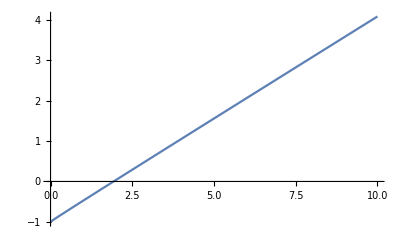

```mathematica
Subscript[y, 0,α_]:=Subscript[y, 0,α]=0;
h=.001;
Ν=1/h;
Subscript[y, 1,α_]:=Subscript[y, 1,α]=h α
Subscript[x, n_]:=Subscript[x, n]=h n
Subscript[y, n_,α_]:=Subscript[y, n,α]=2 Subscript[y, n-1,α]-Subscript[y, n-2,α]+h^2 Subscript[x, n-1] √Subscript[y, n-1,α]
F[α_]:=∫_0^1 Interpolation[Table[{Subscript[x, n],Subscript[y, n,α]},{n,0,Ν}],InterpolationOrder->1][x]ⅆx-1
τ=.1;
range=10;
ListLinePlot[Table[{τ n,F[τ n]},{n,0,range/τ}]]
```

```mathematica
Φ[α]=Interpolation[Table[{τ n,F[τ n]},{n,0,range/τ}],InterpolationOrder->1][α];
sol2=NSolve[Φ[α]==0,α][[1,1]]
```

α→1.92892

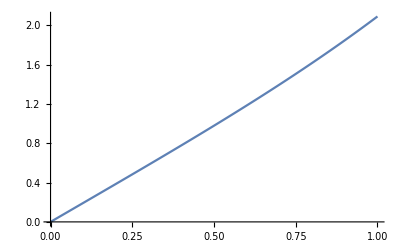

```mathematica
Subscript[y, 0]=0;
Subscript[y, 1]=h α/.sol2;
Subscript[y, n_]:=Subscript[y, n]=2 Subscript[y, n-1]-Subscript[y, n-2]+h^2 Subscript[x, n-1] √Subscript[y, n-1]
ListLinePlot[Table[{Subscript[x, n],Subscript[y, n]}//Flatten,{n,0,Ν}],PlotRange->All]
```

```mathematica
Needs["CellsToTeX`"]
```

```mathematica
testCell=Cell[BoxData[{RowBox[{RowBox[{SubscriptBox["y","0"],"=","0"}],";"}],"
",RowBox[{RowBox[{SubscriptBox["y","1"],"=",RowBox[{RowBox[{"h"," ","α"}],"/.","sol2"}]}],";"}],"
",RowBox[{SubscriptBox["y","n_"],":=",RowBox[{SubscriptBox["y","n"],"=",RowBox[{RowBox[{"2",SubscriptBox["y",RowBox[{"n","-","1"}]]}],"-",SubscriptBox["y",RowBox[{"n","-","2"}]],"+",RowBox[{SuperscriptBox["h","2"],SubscriptBox["x",RowBox[{"n","-","1"}]],SqrtBox[SubscriptBox["y",RowBox[{"n","-","1"}]]]}]}]}]}],"
",RowBox[{"ListLinePlot","[",RowBox[{RowBox[{"Table","[",RowBox[{RowBox[{RowBox[{"{",RowBox[{SubscriptBox["x","n"],",",SubscriptBox["y","n"]}],"}"}],"//","Flatten"}],",",RowBox[{"{",RowBox[{"n",",","0",",","Ν"}],"}"}]}],"]"}],",",RowBox[{"PlotRange","→","All"}]}],"]"}]}],"Input",CellChangeTimes->{{3.825099351272582*^9,3.8250994109323597*^9},{3.8250994580460463*^9,3.825099475218305*^9},{3.82509950761348*^9,3.825099582093889*^9},{3.825099735282943*^9,3.825099761091473*^9},{3.825099798549633*^9,3.825099827680264*^9},{3.825099941900806*^9,3.825099944299774*^9},{3.825099984955571*^9,3.8250999858243923*^9},{3.8251000308900213*^9,3.825100045250579*^9},{3.825100081862797*^9,3.825100083879178*^9},{3.825100119298224*^9,3.82510018924227*^9},{3.825100313864984*^9,3.8251003191979322*^9}},CellLabel->"In[166]:="]











CellToTeX[testCell]
```

Cell[BoxData[{RowBox[{RowBox[{SubscriptBox[y,0],=,0}],;}],
,RowBox[{RowBox[{SubscriptBox[y,1],=,RowBox[{RowBox[{h, ,α}],/.,sol2}]}],;}],
,RowBox[{SubscriptBox[y,n_],:=,RowBox[{SubscriptBox[y,n],=,RowBox[{RowBox[{2,SubscriptBox[y,RowBox[{n,-,1}]]}],-,SubscriptBox[y,RowBox[{n,-,2}]],+,RowBox[{SuperscriptBox[h,2],SubscriptBox[x,RowBox[{n,-,1}]],SqrtBox[SubscriptBox[y,RowBox[{n,-,1}]]]}]}]}]}],
,RowBox[{ListLinePlot,[,RowBox[{RowBox[{Table,[,RowBox[{RowBox[{RowBox[{{,RowBox[{SubscriptBox[x,n],,,SubscriptBox[y,n]}],}}],//,Flatten}],,,RowBox[{{,RowBox[{n,,,0,,,Ν}],}}]}],]}],,,RowBox[{PlotRange,→,All}]}],]}]}],Input,CellChangeTimes→{{3.8251×10^9,3.8251×10^9},{3.8251×10^9,3.8251×10^9},{3.8251×10^9,3.8251×10^9},{3.8251×10^9,3.8251×10^9},{3.8251×10^9,3.8251×10^9},{3.8251×10^9,3.8251×10^9},{3.8251×10^9,3.8251×10^9},{3.8251×10^9,3.8251×10^9},{3.8251×10^9,3.8251×10^9},{3.8251×10^9,3.8251×10^9},{3.8251×10^9,3.8251×10^9}},CellLabel→In[166]:=]

\begin{mmaCell}[moredefined={h},morepattern={n_, n}]{Input}
  \mmaSub{y}{0}=0;
  \mmaSub{y}{1}=h \mmaUnd{\(\pmb{\alpha}\)}/.sol2;
  \mmaSub{y}{n_}:=\mmaSub{y}{n}=2\mmaSub{y}{n-1}-\mmaSub{y}{n-2}+\mmaSup{h}{2}\mmaSub{x}{n-1}\mmaSqrt{\mmaSub{y}{n-1}}
  ListLinePlot[Table[\{\mmaSub{x}{\mmaFnc{n}},\mmaSub{y}{\mmaFnc{n}}\}//Flatten,\{\mmaFnc{n},0,\mmaDef{N}\}],PlotRange\(\pmb{\to}\)All]
\end{mmaCell}

```mathematica
Subscript[x, i]^2
```

```mathematica
SetOptions[CellToTeX,"CurrentCellIndex"->Automatic];
ExportString[NotebookGet[nbObj]/.cell:Cell[_,__]:>Cell[CellToTeX[cell],"Final"],"TeX","FullDocument"->False,"ConversionRules"->{"Final"->Identity}]
```

TeXForm::unspt: TeXForm of … is not supported.

TeXForm::unspt: TeXForm of InlineGraphicBox[GraphicsBox[«1»]] is not supported.

TeXForm::unspt: TeXForm of … is not supported.

General::stop: Further output of TeXForm::unspt will be suppressed during this calculation.

```mathematica
Needs["CellsToTex`"]
```

Get::noopen: Cannot open CellsToTex`.

Needs::nocont: Context CellsToTex` was not created when Needs was evaluated.

$Failed

```mathematica
nbObj=CreateDocument[{{Cell[CellGroupData[{Cell[BoxData[{RowBox[{RowBox[{RowBox[{"Φ","[","α","]"}],"=",RowBox[{RowBox[{"Interpolation","[",RowBox[{RowBox[{"Table","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"τ"," ","n"}],",",RowBox[{"F","[",RowBox[{"τ"," ","n"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"n",",","0",",",FractionBox["range","τ"]}],"}"}]}],"]"}],",",RowBox[{"InterpolationOrder","→","1"}]}],"]"}],"[","α","]"}]}],";"}],"
",RowBox[{"sol2","=",RowBox[{RowBox[{"NSolve","[",RowBox[{RowBox[{RowBox[{"Φ","[","α","]"}],"==","0"}],",","α"}],"]"}],"[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}]}]}],"Input",CellChangeTimes->{{3.8250982223422127*^9,3.825098227732671*^9},{3.8250984344915743*^9,3.825098440113613*^9},{3.825098993078826*^9,3.825099083136085*^9},{3.825100291145108*^9,3.825100292733678*^9}},CellLabel->"In[164]:="],Cell[BoxData[RowBox[{"α","→","1.9289171994367615`"}]],"Output",CellChangeTimes->{3.8250982346403418*^9,3.825098287936864*^9,{3.825098431057818*^9,3.82509843527335*^9},3.825099094508667*^9,3.8251000703418016*^9,3.8251002945082083*^9},CellLabel->"Out[165]="]},Open]],Cell[BoxData[{RowBox[{RowBox[{SubscriptBox["y","0"],"=","0"}],";"}],"
",RowBox[{RowBox[{SubscriptBox["y","1"],"=",RowBox[{RowBox[{"h"," ","α"}],"/.","sol2"}]}],";"}],"
",RowBox[{SubscriptBox["y","n_"],":=",RowBox[{SubscriptBox["y","n"],"=",RowBox[{RowBox[{"2",SubscriptBox["y",RowBox[{"n","-","1"}]]}],"-",SubscriptBox["y",RowBox[{"n","-","2"}]],"+",RowBox[{SuperscriptBox["h","2"],SubscriptBox["x",RowBox[{"n","-","1"}]],SqrtBox[SubscriptBox["y",RowBox[{"n","-","1"}]]]}]}]}]}],"
",RowBox[{"ListLinePlot","[",RowBox[{RowBox[{"Table","[",RowBox[{RowBox[{RowBox[{"{",RowBox[{SubscriptBox["x","n"],",",SubscriptBox["y","n"]}],"}"}],"//","Flatten"}],",",RowBox[{"{",RowBox[{"n",",","0",",","Ν"}],"}"}]}],"]"}],",",RowBox[{"PlotRange","→","All"}]}],"]"}]}],"Input",CellChangeTimes->{{3.825099351272582*^9,3.8250994109323597*^9},{3.8250994580460463*^9,3.825099475218305*^9},{3.82509950761348*^9,3.825099582093889*^9},{3.825099735282943*^9,3.825099761091473*^9},{3.825099798549633*^9,3.825099827680264*^9},{3.825099941900806*^9,3.825099944299774*^9},{3.825099984955571*^9,3.8250999858243923*^9},{3.8251000308900213*^9,3.825100045250579*^9},{3.825100081862797*^9,3.825100083879178*^9},{3.825100119298224*^9,3.82510018924227*^9},{3.825100313864984*^9,3.8251003191979322*^9}},CellLabel->"In[166]:="]}

}];
(*Swich off auto deleting of labels,so that we can extract some data from them.*)
CurrentValue[nbObj,CellLabelAutoDelete]=False;
SelectionMove[nbObj,All,Notebook];
SelectionEvaluate[nbObj,Before];
```